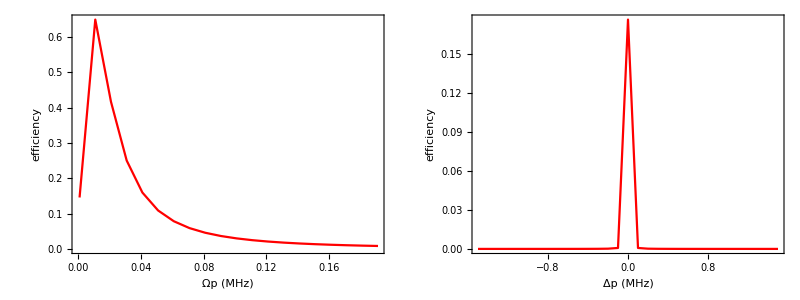

```mathematica
Clear["Global`*"]
LegFon="Helvetica";
PloFon="Helvetica";
PloFonSiz=14;
LegFonSiz=13;
Off[General::"spell1"]
SetOptions[ListPlot,DisplayFunction->Identity,Frame->True,PlotRange->All,BaseStyle->{FontFamily->PloFon,FontSize->PloFonSiz,FontColor->Black},FrameStyle->Directive[Thickness[0.005],Black],TicksStyle->Thick];
SetOptions[ListLinePlot,DisplayFunction->Identity,Frame->True,PlotRange->All,BaseStyle->{FontFamily->PloFon,FontSize->PloFonSiz,FontColor->Black},FrameStyle->Directive[Thickness[0.005],Black],TicksStyle->Thick];
SetOptions[ListDensityPlot,DisplayFunction->Identity,PlotRange->All,Mesh->False,BaseStyle->{FontFamily->"Arial",FontSize->14}];
SetOptions[DensityPlot,DisplayFunction->Identity,PlotRange->All,Mesh->False,BaseStyle->{FontFamily->PloFon,FontSize->PloFonSiz}];
SetOptions[Plot,DisplayFunction->Identity,PlotRange->All,Frame->True,(*PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1]},*)BaseStyle->{FontFamily->PloFon,FontSize->PloFonSiz},FrameStyle->Directive[Thickness[0.005],Black],TicksStyle->Thick];
SetOptions[LogLogPlot,DisplayFunction->Identity,PlotRange->All,Frame->True,(*PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1]},*)BaseStyle->{FontFamily->PloFon,FontSize->PloFonSiz},FrameStyle->Directive[Thickness[0.005],Black],TicksStyle->Thick];
SetOptions[Plot3D,DisplayFunction->$DisplayFunction,PlotRange->All,BaseStyle->{FontFamily->"Arial",FontSize->14}];
SetOptions[ContourPlot,ContourStyle->None,DisplayFunction->$DisplayFunction,PlotRange->All,BaseStyle->{FontFamily->"Arial",FontSize->14},FrameStyle->Black];
WorkingPrecision->(2 MachinePrecision);
Nblevels=4;
ReH={{0,Re[Ωp]/2,0,Re[ΩL]/2},{Re[Ωp]/2,0,Re[Ωm]/2,0},{0,Re[Ωm]/2,0,Re[Ωc]/2},{Re[ΩL]/2,0,Re[Ωc]/2,0}};
ImH={{0,(-Im[Ωp])/2,0,(-Im[ΩL])/2},{Im[Ωp]/2,0,(-Im[Ωm])/2,0},{0,Im[Ωm]/2,0,Im[Ωc]/2},{Im[ΩL]/2,0,-Im[Ωc]/2,0}};

Reρρ[t_]=Table[Reρ[i,j][t],{i,Nblevels},{j,1,Nblevels}];
Do[
Reρ[i,j][t]=Reρ[j,i][t],
{i,Nblevels},{j,1,i-1}
];

Imρρ[t_]=Table[Imρ[i,j][t],{i,Nblevels},{j,1,Nblevels}];
Do[
Imρ[i,j][t]=-Imρ[j,i][t],
{i,Nblevels},{j,1,i-1}
];

Do[Imρ[i,i][t]=0,{i,1,Nblevels}];

Delta =- DiagonalMatrix[{0,Δp,0,0}];

ReH=ReH+Delta;
Delta//MatrixForm;
ReH//MatrixForm;
ImH//MatrixForm;

TotalH=ReH+ⅈ ImH//MatrixForm;
ReB=(ReH.Imρρ[t]-Imρρ[t].ReH)+(ImH.Reρρ[t]-Reρρ[t].ImH);
ImB=-(ReH.Reρρ[t]-Reρρ[t].ReH)+(ImH.Imρρ[t]-Imρρ[t].ImH);

GammaSpont=IdentityMatrix[Nblevels];
GammaSpont[[1,1]]=0;
GammaSpont[[2,2]]=γ;
GammaSpont[[3,3]]=γ;
GammaSpont[[4,4]]=Γ;

ReLoss=-1/2(GammaSpont.Reρρ[t]+Reρρ[t].GammaSpont);
ReLoss//MatrixForm;
ImLoss=-1/2(GammaSpont.Imρρ[t]+Imρρ[t].GammaSpont);
ImLoss//MatrixForm;


ReLoss[[1,1]]=ReLoss[[1,1]]+γ Reρ[2,2][t]+Γ Reρ[4,4][t];
ReLoss[[4,4]]=ReLoss[[4,4]]+γ Reρ[3,3][t];


For[ii=1, ii≤ 4, ii++,
If[ii≠ 2,
ReLoss[[2,ii]]-= γ2d Reρ[2,ii][t];
ReLoss[[ii,2]]-= γ2d Reρ[2,ii][t];
ImLoss[[ii,2]]-=γ2d Imρ[ii,2][t];
ImLoss[[2,ii]]+=γ2d Imρ[ii,2][t];
]
]

For[ii=1, ii≤ 4, ii++,
If[ii≠ 3,
ReLoss[[3,ii]]-= γ3d Reρ[3,ii][t];
ReLoss[[ii,3]]-= γ3d Reρ[3,ii][t];
ImLoss[[ii,3]]-=γ3d Imρ[ii,3][t];
ImLoss[[3,ii]]+=γ3d Imρ[ii,3][t];
]
]

ReLoss//MatrixForm;
ReA=FullSimplify[ReB+ReLoss];
ImA=FullSimplify[ImB+ImLoss];
ReA//MatrixForm;
(ReB+ReLoss)//MatrixForm;
eqnsDifRe2=Flatten[
Table [
Simplify[ReA[[i,j]]==0,(Reρ[i,j][t])∈Reals&&(Imρ[i,j][t])∈Reals&&(Reρ[j,i][t])∈Reals&&(Imρ[j,i][t])∈Reals],
{i,1,Nblevels},{j,i,Nblevels}
]
];
eqnsDifIm1=Flatten[Table [Simplify[ImA[[i,j]]==0,(Reρ[i,j][t])∈Reals&&(Imρ[i,j][t])∈Reals&&(Reρ[j,i][t])∈Reals&&(Imρ[j,i][t])∈Reals],{i,1,Nblevels},{j,i+1,Nblevels}]];
eqnstime=Join[eqnsDifRe2,eqnsDifIm1];
eqnstime[[1]];
VariablesSolve2=Join[
Flatten[Table[(Reρ[i,i][t]),{i,1,Nblevels}]],
Flatten[Table[(Reρ[i,j][t]),{i,1,Nblevels},{j,i+1,Nblevels}]],
Flatten[Table[(Imρ[i,j][t]),{i,1,Nblevels},{j,i+1,Nblevels}]]];

variablesList=Table[
{ii,VariablesSolve2[[ii]]},
{ii,1,Length[VariablesSolve2]}
];
variablesList//TableForm;
MatrixCoef2=CoefficientArrays[eqnstime,VariablesSolve2];
MM2=Normal[MatrixCoef2][[2]];
Y2=-Normal[MatrixCoef2][[1]];
eqnsDifRe2check=MM2.VariablesSolve2;
ReA[[1,1]];
eqnsDifRe2check[[1]];
Coef2=Simplify[ReA[[1,1]]/eqnsDifRe2check[[1]]];
MM2=MM2*Coef2;
Y2=Y2*Coef2;
Y2[[1]]=1;
MM2[[1]]=Table[0,{i,1,Length[VariablesSolve2]}];
MM2[[1]][[1;;Nblevels]]=Table[1,{i,1,Nblevels}];
MM2//MatrixForm;
Y2//MatrixForm;
solution:=LinearSolve[MM2,Y2];
Num1[ΩpIn_,nat_,wz_,ΩmIn_,ΩcIn_,ΔpIn_,ΔmIn_,ΔcIn_,γ2dIn_,γ3dIn_]:=Module[
{Iout={},zz=-2.8*wz,Deltazz=wz/1000,
Ωpout=10^9 ΩpIn,ΩLSignal=10^9 ΩL0,ΩcCalc=10^9 ΩcIn,ΩmCalc=10^9 ΩmIn,
constA,constB},
constA=nat 1/(ℏ ϵ0 c);
constB=1/2 ϵ0 c ℏ^2;

(* define detunings *)
Δp=ΔpIn;
Δm=ΔmIn;Δc=ΔcIn;
(* define dephasing parameters *)
γ2d=γ2dIn;
γ3d=γ3dIn;

(* numerically solve 1D equation *)
While[(zz<=(2.8*wz)),

(* for the calculation of the density matrix, the unit of GHz is assumed, for the propagation diff equation, SI units are used *)
Ωp=Ωpout/10^9;
ΩL=ΩLSignal/10^9;
Ωc=ΩcCalc/10^9;
Ωm=ΩmCalc/10^9;
solutionTemp=solution;
ρ1S=solutionTemp[[1]];
ρ2S=solutionTemp[[2]];
ρ3S=solutionTemp[[3]];
ρ4S=solutionTemp[[4]];
Imρ12S=solutionTemp[[11]];
Imρ13S=solutionTemp[[12]];
Imρ14S=solutionTemp[[13]];
Imρ23S=solutionTemp[[14]];
Imρ34S=solutionTemp[[16]];
Reρ12S=solutionTemp[[5]];
Reρ13S=solutionTemp[[6]];
Reρ14S=solutionTemp[[7]];
Reρ23S=solutionTemp[[8]];
Reρ34S=solutionTemp[[10]];


Ωpout=Ωpout-ⅈ ⅇ^(-2 zz^2/wz^2)*Deltazz*constA d12^2 ωP*(-ⅈ Imρ12S + Reρ12S);
ΩLSignal=ΩLSignal-ⅈ ⅇ^(-2 zz^2/wz^2)*Deltazz*constA d14^2 ωL(-ⅈ Imρ14S + Reρ14S);
ΩmCalc=ΩmCalc-ⅈ ⅇ^(-2 zz^2/wz^2)*Deltazz*constA d23^2 ωM (-ⅈ Imρ23S + Reρ23S );
ΩcCalc=ΩcCalc -ⅈ ⅇ^(-2 zz^2/wz^2)*Deltazz*constA d34^2 ωC (+ⅈ Imρ34S + Reρ34S );

Iout=AppendTo[Iout,{zz,(constB/d14^2  Abs[ΩLSignal]^2/((constB/d23^2)  Abs[10^9 ΩmIn]^2)) (ωM/ωL)}];
zz=zz+Deltazz];

Iout]
DefineParam1:=Module[{res},ϵ0=8.85*10^(-12);
c=2.9979*10^8;
h=6.626*10^(-34);
elcharge=1.6021766208 10^-19;
a0=0.5292*10^(-10);
Eua=4.36*10^(-18); 
ℏ=h/(2π);
μm=10^(-6);
Mp=1.6726231*10^-27;Mat=133 Mp;kB=1.3806503*10^-23;
λp=0.319 10^-6;
λc=0.510 10^-6;
λL=0.852 10^-6;
σ0=3 λp^2/(2 π);
wz0=1*10^-3;
wp0=50 10^-6;
wc0=47 10^-6;
ωL=2π c/λL;
ωP=2π c/λp;
ωC=2π c/λc;
ωM=2π 9.9 10^9;
Is=16.67;
nat0=OD0/(Sqrt[π/2] wz0 σ0);
d12=0.003 elcharge a0;
d14=3.162 elcharge a0;
d34=0.025elcharge a0;
d23=1137.443elcharge a0;
Γ=2 π 5.22*10^-3;
δ0=0*2 π*10^-3;
res=0;res];
DefineParam1;
Ωp0=2 π 0.0011119*1 10^-3;Ωm0=2 π *0.01 10^-3;Ωc0=2 π*36.58 10^-3;ΩL0=0.0 2 π *6.01 10^-3;OD0=5;γd=2 π 0.001 10^-3;
γ2d=γd;γ3d=γd;γ=2 π 0.01 10^-3;γ2=γ;γ3=1*γ;Δp=0*2 π*10^-3;
evsOp=Table[Flatten[{Ωp/(2*π)10^3,Last[Num1[Ωp,OD0 √(2/π)1/wz0 1/σ0,wz0,Ωm0,Ωc0,Δp,Δm,Δc,γ2d,γ3d]]}],{Ωp,0.001*2π*10^-3,0.2*2π*10^-3,0.01*2π*10^-3}];
evsdp=Table[Flatten[{Δp/(2*π)10^3,Last[Num1[Ωp0,OD0 √(2/π)1/wz0 1/σ0,wz0,Ωm0,Ωc0,Δp,Δm,Δc,γ2d,γ3d]]}],{Δp,-1.5*2π*10^-3,1.5*2π*10^-3,0.1*2π*10^-3}];
p1 =ListLinePlot[{evsOp[[1;;,{1,3}]]},PlotStyle->{Red},ImageSize->Medium,FrameLabel->{{"efficiency  ",""},{"Ωp (MHz)",""}}];
p2 =ListLinePlot[{evsdp[[1;;,{1,3}]]},PlotStyle->{Red},ImageSize->Medium,FrameLabel->{{"efficiency  ",""},{"Δp (MHz)",""}}];
Grid[{{p1,p2}}]
(*Plot3D[{Last[Num1[Ωp/(2*π)10,OD0 √(2/π)1/wz0 1/σ0,wz0,Ωm0,Ωc0,Δp/(2*π)10^3,Δm,Δc,γ2d,γ3d]]},{Ωp,0.1*2π*10^-3,0.11*2π*10^-3},{Δp,0*2π*10^-3,0.1*2π*10^-3},Mesh->All]*)
```